```mathematica
Clear["`*"]
```

```mathematica
visualize[pt_, bounds_, f_, slopes_] := Animate[Plot[f[x], {x, -Max[Abs[#]&/@Flatten[bounds]], Max[Abs[#]&/@Flatten[bounds]]}, 
	PlotRange -> Max[Abs[f[#]]&/@Flatten[bounds]] + 1,
	Epilog-> If[i >= Length[bounds], {PointSize[Large], Point[{pt, 0}], Style[Text[ToString[{N[pt], N[f[pt]]}], {pt, 0}, {-1, -2}], Bold]},
		Join[{Pink, PointSize[0.02]}, Point[{#, f[#]}]&/@bounds[[i]], 
			InfiniteLine[{bounds[[i]][[#]], f[bounds[[i]][[#]]]}, slopes[[i]][[#]]]&/@Range[Length[bounds[[i]]]]]
]], {i, 1, Length[bounds]+2, 1}, AnimationRunning -> False, AnimationRepetitions -> 2]
```

```mathematica
bisect = Function[{f, intervalStart, intervalEnd, iterationsLimit, minInterval, precision}, 
	Clear[root, bounds];
	root = intervalStart + (intervalEnd - intervalStart)/2;
	bounds = {{intervalStart, intervalEnd}};
	Begin["bisect`"]; 
	start = intervalStart;
	end = intervalEnd;
	valueAtStart = f[start];
	valueAtEnd = f[end];
	width = end - start;
	If[Sign[valueAtStart] != Sign[valueAtEnd], 
		width /= 2;
		mid = start + width;
		midValue = f[mid];
		For[i = 0, i < iterationsLimit && Abs[width] >= minInterval && Abs[midValue] >= precision, ++i,
			root = mid;
			If[Sign[valueAtStart] != Sign[midValue], 
				end = mid;
				valueAtEnd = midValue;
				,
				start = mid;
				valueAtStart = midValue;
			];
			AppendTo[bounds, {start, end}];
			width /= 2;
			mid = start + width;
			midValue = f[mid];
		];
	];
	End[];
	{root, bounds}
];
```

```mathematica
Clear[fn]
fn[x_]:=x^2 - 4x * Sin[x] - Pi^x - 5
{pt, bounds} = bisect[fn, -10, 2, 100, 10^-5, 0.01];
visualize[pt, bounds, fn, {{0, 1}, {0, 1}}&/@Range[Length[bounds]]]
```

```mathematica
newtonRawson = Function[{f, around, iterationsLimit, minInterval, precision},
	root = around;
	approximations = {};
	slopes = {};
	Begin["newtonRawson`"]; 
	midValue = f[root]; 
	width = minInterval;
	df = Derivative[1][f];
	For[i = 0, i < iterationsLimit && Abs[width] >= minInterval && Abs[midValue] >= precision, ++i,
		slope = df[root];
		newRoot = root - midValue/slope;
		width = Abs[newRoot - root];
		AppendTo[approximations, {root, newRoot}];
		root = newRoot;
		AppendTo[slopes, {{1, slope}, {0, 1}}];
		midValue = N[f[root]];
	];
	End[];
	{root, approximations, slopes}
];
```

```mathematica
a=RandomInteger[{#, 10}]&/@Range[6]
fn2=Function[x, a[[1]] x^5 + a[[2]] x^4 + a[[3]] x^3 + a[[4]] x^2 + a[[5]]x + a[[6]]];
{pt, approx, slopes} = newtonRawson[fn2, 1, 30, 10^-4, 0.001];
visualize[pt, approx, fn2, slopes]
```

{8,7,3,7,5,7}

```mathematica
falsi = Function[{fun, intervalStart, intervalEnd, iterationsLimit, minInterval, precision}, 
	Clear[root, bounds];
	bounds = {};
	slopes = {};
	root = intervalEnd;
	Begin["falsi`"]; 
	f[x_]:=N[fun[x]];
	start = intervalStart;
	end = intervalEnd;
	valueAtStart = f[start];
	valueAtEnd = f[end];
	If[Sign[valueAtStart] != Sign[valueAtEnd], 
		For[i=0, i < iterationsLimit && Abs[end - start] >= minInterval && Abs[f[root]] >= precision, ++i,
			a = (valueAtEnd - valueAtStart)/(end - start);
			root = end - valueAtEnd/a;
			AppendTo[bounds, {start, end, root}];
			AppendTo[slopes, {{end - start, valueAtEnd - valueAtStart}, {end - start, valueAtEnd - valueAtStart}, {0, 1}}];
			rootValue = f[root];
			If[Sign[valueAtStart] != Sign[rootValue], 
				end = root;
				valueAtEnd = rootValue;
				,
				start = root;
				valueAtStart = rootValue;
			];
		];	
	];
	End[];
	{root, bounds, slopes}
];
```

```mathematica
Clear[fnf]
fnf[x_]:=x^2 - 4x * Sin[x] - Pi^x - 5
{pt, approx, slopes} = falsi[fnf, -10, 2, 100, 10^-5, 0.01];
visualize[pt, approx, fnf, slopes]
```

```mathematica
riemann = Function[{f, intervalStart, intervalEnd, slicesCount, selector},
	riemannSum = 0.;
	Begin["riemman`"];
	direction = If[intervalStart < intervalEnd, 1, -1];
	start = Min[intervalStart, intervalEnd];
	len=Abs[intervalEnd-intervalStart]/slicesCount;
	For[i = 0, i < slicesCount, ++i,
		end = start + len;
		c = selector[start, end];
		riemannSum += f[c] * Abs[end - start];
		start = end;
	];
	End[];
	direction * riemannSum
];
```

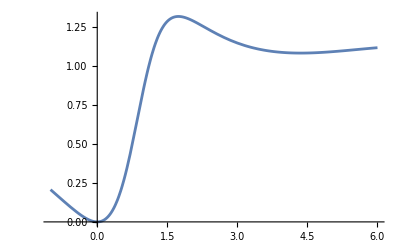

4.90415

4.90411

```mathematica
Clear[fn3];
fn3 = Function[x, x^2/(x^2-x+2-Sin[x])];
start = 0; end = 5;
Plot[fn3[x], {x, start-1, end+1}, PlotRange->Full]
NIntegrate[fn3[x], {x, start, end}]
riemann[fn3, start, end, 1000, Function[{start, end}, RandomReal[{start, end}]]]
```

```mathematica
visualRiemann = Function[{f, intervalStart, intervalEnd, slicesCount, selector}, Animate[
	len=Abs[intervalEnd-intervalStart]/i;
	bounds = (intervalStart + #*len)&/@Range[0, i];
	selected = selector[intervalStart + (# - 1)*len, intervalStart + #*len]&/@Range[i];
	Plot[f[x], {x, intervalStart - 1, intervalEnd + 1}, PlotLabel->StringJoin["Riemann's Sum = ", ToString[riemann[fn3, intervalStart, intervalEnd, i, selector]]],
	Epilog -> Join[
		InfiniteLine[{#, f[#]}, {0,1}]&/@bounds,
		{PointSize[0.012], Red}, 
		Point[{#, f[#]}]&/@selected,
		Line[{{#, f[#]}, {#,0}}]&/@selected
	]], 
{i, 2, slicesCount, 1}, AnimationRepetitions -> 1]];
```

```mathematica
visualRiemann[fn3, 0, 5, 200, Function[{start, end}, RandomReal[{start, end}]]]
```

```mathematica
monteCarlo = Function[{fun, intervalStart, intervalEnd, sampleSize},
	result=0;
	Begin["monteCarloIntegral`"];
	samplesIn = 0;
	f[x_]:=N[fun[x]];
	direction = If[intervalStart < intervalEnd, 1, -1];
	start = Min[intervalStart, intervalEnd];
	end = Max[intervalStart, intervalEnd];
	min = Minimize[{f[z], start <= z <= end}, {z}][[2]][[1]][[2]];
	max = Maximize[{f[z], start <= z <= end}, {z}][[2]][[1]][[2]];
	areaSize = (max - min) * (end - start);
	For[i=0, i < sampleSize, ++i,
		x = RandomReal[{start, end}];
		y = RandomReal[{min, max}];
		If[Abs[y] <= Abs[f[x]], ++samplesIn];
	];
	result = direction * areaSize * samplesIn/sampleSize;
	End[];
	result
];
```

```mathematica
NIntegrate[fn3[x], {x, 0, 5}]
monteCarlo[fn3, 0, 5, 10000]
```

4.90415

4.91491

```mathematica
visualMonteCarlo = Function[{fun, intervalStart, intervalEnd, sampleSize},
	samplesIn = 0;
	f[x_]:=N[fun[x]];
	direction = If[intervalStart < intervalEnd, 1, -1];
	start = Min[intervalStart, intervalEnd];
	end = Max[intervalStart, intervalEnd];
	min = Minimize[{f[z], start <= z <= end}, {z}][[2]][[1]][[2]];
	max = Maximize[{f[z], start <= z <= end}, {z}][[2]][[1]][[2]];
	areaSize = (max - min) * (end - start);
	points = {};
	results = {};
	For[i = 0, i < sampleSize, ++i, 
		x = RandomReal[{start, end}];
		y = RandomReal[{min, max}];
		If[Abs[y] <= Abs[f[x]], ++samplesIn; AppendTo[points, Red], AppendTo[points, Blue]];
		AppendTo[points, Point[{x, y}]];
		AppendTo[results, direction * areaSize * samplesIn/sampleSize];
	];
	Animate[
		Plot[fun[z], {z, intervalStart - 0.1, intervalEnd + 0.1}, PlotRange->Full, PlotLabel->StringJoin["Area = ", ToString[results[[i]]]], Epilog->points[[1 ;; i]]],
		{i, 0, sampleSize, 1}, AnimationRepetitions -> 1
	]
];
```

```mathematica
visualMonteCarlo[fn3, 0, 5, 5000]
```